```mathematica
points = {};
n=20;
For[p= 1, p< n,
points = Append[points, {H*Random[], H*Random[], Sign[Random[]-0.5]}];
p++]
```

```mathematica
W = 100;
H = 100;
field = {};
For[x =1, x≤ W,
For[y=1, y≤ H,
value = 0;
For[i=1, i<= Length[points],
value =value +  points[[i]][[3]]/((points[[i]][[1]]-x)^2+(points[[i]][[2]]-y)^2)^0.2;
i++];
field=Append[field, {x, y, value}];
y++];
x++];
```

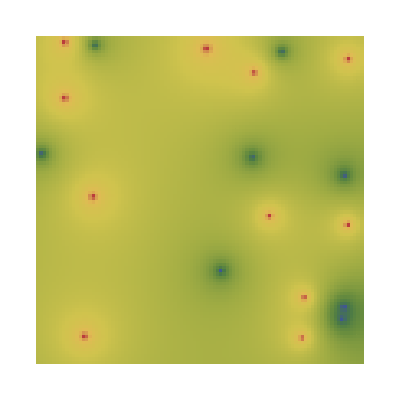

```mathematica
mx=Max[(#[[3]]+1)/2&/@field];
Graphics[{ColorData["DarkRainbow"][(#[[3]]+1)/(2*mx)],Rectangle[{#[[1]], #[[2]]}, {#[[1]]+1, #[[2]]+1}]}&/@field]
```

```mathematica
mx=Max[(#[[3]]+1)/2&/@field];
Manipulate[
Graphics[{ColorData["DarkRainbow"][If[(#[[3]]+1)/(2*mx)>x, 1, 0]],Rectangle[{#[[1]], #[[2]]}, {#[[1]]+1, #[[2]]+1}]}&/@field], {x, 0, 1}]
```

```mathematica
field[[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧